# 电偶极辐射

## 陈可鉴 18 天文 201811160113

设定基本的坐标变量和假设：

```mathematica
cart coord = {x,y,z};
cyl coord = {ρ,ψ,h};
sph coord = {r,θ,ϕ};
$Assumptions = And@@{r>0,ρ>0}
```

r>0&&ρ>0

## 电偶极辐射的电场线

图 5-4 ：
-Graphics-

## 尝试：展开到 R^-1 的电场线

假设电流为时谐的 （Fourier 分量），并且电流分布于小区域内，将矢势在远场处展开，其第一项为电偶极辐射：
-Graphics-

如果按照书上的方式展开，对 R 只展到 R^-1 项，则得到：

-Graphics-
再取球坐标，得   -Graphics-

将电场在球坐标下写出：

```mathematica
E1 sph=p''/(4π Subscript[ε, 0] c^2) Exp[I k r]/r Sin[θ]{0,1,0}/.{p''/(4π Subscript[ε, 0] c^2)->1}
```

{0,(ⅇ^(ⅈ k r) Sin[θ])/r,0}

转换到柱坐标（因为旋转对称性，只需要画切面上的图，因此使用柱坐标）：

```mathematica
E1 cyl=TransformedField["Spherical"->"Cylindrical",E1 sph,sph coord->cyl coord]
```

{(ⅇ^(ⅈ k √(h^2+ρ^2)) h ρ)/((h^2+ρ^2)^(3/2)),0,-(ⅇ^(ⅈ k √(h^2+ρ^2)) ρ^2)/((h^2+ρ^2)^(3/2))}

画出电场线。
可以发现，电场线和我们想要的并不相同。虽然同样随着 r 而有正负方向变化，但是电场只有 θ 分量，电场线不闭合。
究其原因，是因为在计算矢势的展开式时，只取了 R^-1 ，丢掉了高阶项，从而丢弃了沿 r 方向的分量，电场完全为横向，电场线无法闭合。

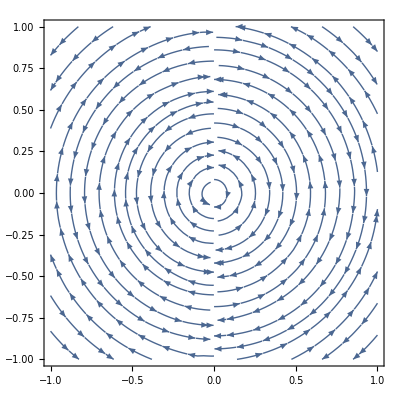

```mathematica
StreamPlot[Re[E1 cyl/.k->15]⟦{1,3}⟧,{ρ,-1,1},{h,-1,1}]
```

在球坐标下计算电场的散度，可以发现其散度不为 0，电场线也因而不闭合。

```mathematica
Div[E1 sph,sph coord,"Spherical"]
```

(2 ⅇ^(ⅈ k r) Cos[θ])/r^2

## 完整的电偶极辐射场

因此，为了画出如图 5-4 那样的电场线，需要使用完整的矢势展开式（仍然有远场近似）。
这里 A 是磁矢势的振幅大小（标量），取前面的系数为 1

```mathematica
A=Subscript[μ, 0]/(4π)Exp[I k r]/r p'/.{Subscript[μ, 0]/(4π)p'->1};
```

将电偶极矩的方向矢量从直角坐标转换到球坐标，从而得到球坐标下的磁矢势：

```mathematica
Avec sph=A * TransformedField["Cartesian"->"Spherical",{0,0,1},cart coord->sph coord]
```

{(ⅇ^(ⅈ k r) Cos[θ])/r,-(ⅇ^(ⅈ k r) Sin[θ])/r,0}

在球坐标下，计算磁矢势的旋度，得到磁场：

```mathematica
Bvec sph=Curl[Avec sph,sph coord,"Spherical"]
```

{0,0,(ⅇ^(ⅈ k r) Sin[θ])/r^2-(ⅈ ⅇ^(ⅈ k r) k Sin[θ])/r}

再在球坐标下计算磁场的旋度，并乘以 i ，得到电场：

```mathematica
Evec sph=I c/k Curl[Bvec sph,sph coord,"Spherical"]/.{c->1}//Simplify
```

{(2 ⅇ^(ⅈ k r) (ⅈ+k r) Cos[θ])/(k r^3),(ⅇ^(ⅈ k r) (ⅈ+k r-ⅈ k^2 r^2) Sin[θ])/(k r^3),0}

可以看到，电场除了在极角方向的 r^-1 阶项，还有在径向和极角方向的 r^-2、r^-3 项，这些项保证了电场线的闭合。

```mathematica
Evec sph//Expand
```

{(2 ⅈ ⅇ^(ⅈ k r) Cos[θ])/(k r^3)+(2 ⅇ^(ⅈ k r) Cos[θ])/r^2,(ⅈ ⅇ^(ⅈ k r) Sin[θ])/(k r^3)+(ⅇ^(ⅈ k r) Sin[θ])/r^2-(ⅈ ⅇ^(ⅈ k r) k Sin[θ])/r,0}

为了画图，将电场转换到柱坐标下。

```mathematica
Evec cyl=TransformedField["Spherical"->"Cylindrical",Evec sph,sph coord->cyl coord]//FullSimplify;
```

定义对应于不同 k 的电场函数，再定义两个用于画图的函数，分别绘制电场线和电场振幅等高线。
电场线的颜色对应于电场强度的平方根
电场振幅等高线与电场线的形状有点类似，但实际上并不相同。

```mathematica
Efield=Function[{k,ρ,h},Evaluate@Re[Evec cyl⟦{1,3}⟧]];
streamplot[k_/;k>0]:=StreamPlot[Efield[k,ρ,h],{ρ,-1,1},{h,-1,1},
StreamPoints->{Automatic,Scaled[.01]},StreamScale->{Automatic,All,Automatic},StreamColorFunction->(ColorData["DeepSeaColors"]@√#5&),PlotLabel->"k = "<>ToString[k]<>" 时的电场线"]//Quiet
contourplot[k_]:=ContourPlot[Norm@Efield[k,ρ,h],{ρ,-1,1},{h,-1,1},
Contours->20,PlotRange->Automatic,PlotLabel->"k = "<>ToString[k]<>" 时的电场振幅"]//Quiet
graphics row[k_]:=GraphicsRow[{streamplot[k],contourplot[k]},ImageSize->800]
```

绘制 k=1~20 对应的电场线和电场振幅，耗时约 90s。

```mathematica
plot list=Table[graphics row[k],{k,1,20,1}];
```

取几个代表性的图展示：
实际上，k 的放大等价于绘图范围的放大，因此这些图实际上是从不同的尺度上来看辐射场。
可以看到：在 kr 较小时，辐射场的特征不太明显；
当 kr 在 1~10 左右时，处在过渡地带，振幅在赤道附近更大，在两极较小。电场的纵向分量仍然存在。
当 kr 较大时，电场纵向分量趋于0，横场占主导，电场线基本完全沿 θ 方向，电磁波趋于 TEM 波。这也就是如前所示的 R^-1 项占主导的结果。

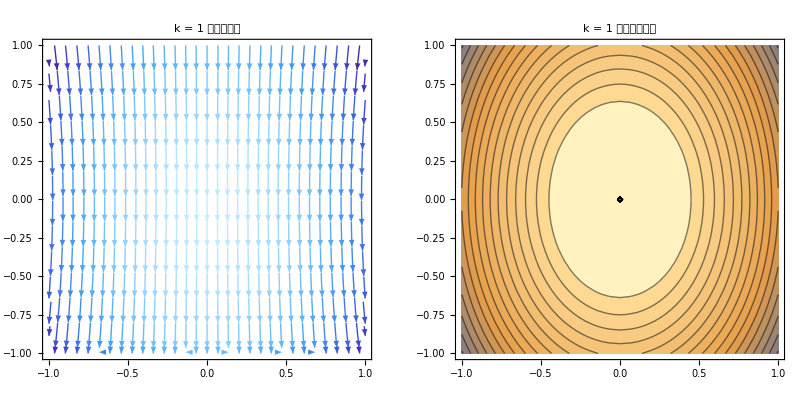
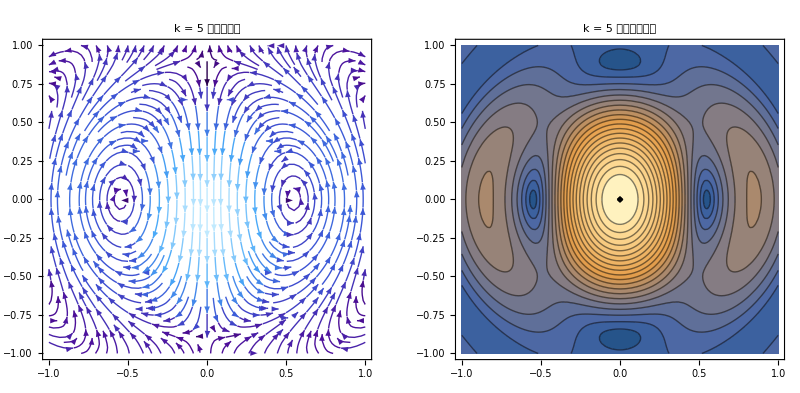
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot list⟦{1,5,10,20}⟧
```

制作动画，以交互式地调整 k 的值。

```mathematica
ListAnimate[plot list,AnimationRunning->False]
```

```mathematica
Export["/Users/chenkejian/Library/Mobile Documents/com~apple~CloudDocs/北师大/物理/四大力学/电动力学/作业/电偶极辐射/plot_list.mov",plot list,FrameRate->4]
```

/Users/chenkejian/Library/Mobile Documents/com~apple~CloudDocs/北师大/物理/四大力学/电动力学/作业/电偶极辐射/plot_list.mov

## 能流密度

能流密度随着 r^-2 衰减，仅需要画出其角分布：
（这里和书上的图比旋转了 90 度）

```mathematica
PolarPlot[Sin[θ]^2,{θ,0,2π},PolarAxes->Automatic,PolarTicks->{"Degrees",Automatic},PlotRange->1.2{{-1,1},{-1,1}},PolarAxesOrigin->{Pi/2, 1},PolarGridLines->Automatic]
```

-Graphics-

使用 NotebookPrint 打印，输出精度更好：

```mathematica
NotebookPrint[ic3e7_shm124FrontEndObject[LinkObject["ic3e7_shm", 3, 1]]124"电偶极辐射.nb""/Users/chenkejian/Library/Mobile Documents/com~apple~CloudDocs/北师大/","/Users/chenkejian/Library/Mobile Documents/com~apple~CloudDocs/北师大/物理/四大力学/电动力学/作业/电偶极辐射/电偶极辐射.pdf"]
```